## Quantum Coherence and Optimal Chromophore Organization for Light Harvesting

This program intends to be the final version of the investgation on the nature of photoexcitations in its relatedness to the optimal arrangements, which is my research topic in Mar. 2010 - 2011.

The program is devided into four parts, the fisrt part setup initial conditions for relevent parameters, the second part calculates the line shape under Drude spectal density, the third part is the core program for calcualting the FRET and MC-FRET rates and relevent data, where as the final part shows the figures needed for study.


Note for an healthy attitide of doing research, a timeline record in writing this program is necessary, and all the odds and ends will be listed at the end.

## Main program

```mathematica
Clear["Global`*"]
```

```mathematica
(* Load needed libraries *)
Needs["VectorAnalysis`"]
Needs["PhysicalConstants`"]

(* define global variables *)
(* size = full state # of the D+A system; dsize = # of donor states *)
size=4;dsize=2;asize=size-dsize; 

(* site energies in cm^-1 *)
E1=13000.;E2=12900.;E3=12300.;E4=12200.;
ener={E1,E2,E3,E4};
R1=40.;R2=r2;τt=10^-12;C2=c2;
r={{-R1/2,0,0},{-R1/2+R2,0,0},{R1/2-R2,0,0},{R1/2,0,0}};
pspherical={{1.,C2,0},{1.,C2,0},{1.,0,0},{1.,0,0}};
p=Table[CoordinatesToCartesian[pspherical[[i]],Spherical],{i,1,size}];

(* when the dipoles are mutually 10 angstroms near,they have coupling energy at 300 wavenumber.*)
const=300000;
(* to calculate coupling via dipole-dipole interaction *)
coup[i_,j_]:=const 1/Norm[r[[i]]-r[[j]]]^3 (p[[i]].p[[j]]-3 (p[[i]].Normalize[r[[i]]-r[[j]]]) (p[[j]].Normalize[r[[i]]-r[[j]]]));
(* 2011.04.03 changed the definition of this function >> uniforms the vector r[[i]]-r[[j]] to eliminate ambiguity *)

hbar=5.30924086117*10^-12;(*in cm^-1 sec*)(*or PlanckConstantReduced*)


β=(0.69*300.)^-1;ℏ=1.;γ=53.;λ=35.;trnk=30.;
(* β: inverse temperature in cm; γ in cm^-1: inverse of bath correlation time -> 53 cm^-1~100 fs; λ is reorganization energy in cm^-1 *)
(* trnk is the truncate level in Matsuraba frequencies, after which the terms are just trivial δ-functions *)
(* parameters refer to S. Mukamel Chem.Rev.2009,109,2350–2408 *)

(* number of sampling realizations *)
realn=1;
(* disorder assignment: 1 -> open; 0 -> no disorder *)
noiseE=0;noiseR=0;noiseμ=0;noiseθ=0;noiseϕ=0;(*No need to open fluc in r,because this may generate unphysical pictures using the theory*)
varR=1;varμ=0.5;varθ=π;varϕ=2π;varE=20;


(* define functions for calculating rate constants *)
(* for doing cluster-diagonalization *)
hamc[hh_]:=Module[{partd=Eigenvectors[hh⟦1;;dsize,1;;dsize⟧],parta=Eigenvectors[hh⟦dsize+1;;size,dsize+1;;size⟧]},
{
mixd=ArrayFlatten[{{partd,0},{0,IdentityMatrix[size-dsize]}}];
mixa=ArrayFlatten[{{IdentityMatrix[dsize],0},{0,parta}}];
Flatten[PadRight[{Total[(partd^4)ᵀ],Total[(parta^4)ᵀ]}]],
Abs[Flatten[{Total@(partdᵀ),Total@(partaᵀ)}]],
Chop[mixa.(mixd.hh.mixdᵀ).mixaᵀ]}](* effective dipole strength Donors/Acceptors: higher energy states to lower *);


(* spectra related functions *)
(*reorg=NIntegrate[2/π(λ γ)/(ω^2+γ^2),{ω,0,∞}];*)
(* define Matsuraba frequencies *)
ν[κ_]:=If[κ==0,γ,(2π κ)/(β ℏ)]

(* define coefficients for the bath time correlation function *)
ca[k_]:=If[k==0,( λ π γ/ℏ^2)( Cot[(β ℏ γ)/2]-ⅈ),((4 π λ γ)/(β ℏ^3))(ν[k]/((ν[k])^2-γ^2))]
crf[t_,Κ_]:=ParallelSum[ca[k]Exp[-ν[k]t],{k,0,Κ,1}]

(* high-T limit *)
(*crf[t_,trnk_]:=((2π λ)/(ℏ β)Exp[-γ t]-1.ⅈ λ γ π Exp[-γ t])*)

(* define the one-sided Fourier transform for the dissipation kernel *)
fcf[ω_]=Assuming[{ω∈Reals && Re[γ]>0},Integrate[crf[t,trnk]Exp[+ⅈ ω t],{t,0,∞}]];
fcfc[ω_]=Assuming[{ω∈Reals && Re[γ]>0},Integrate[crf[t,trnk]Exp[-ⅈ ω t],{t,0,∞}]];
(*Plot[{Re[fcf[ω]],Im[fcf[ω]]},{ω,-1000.,1000.},PlotRange->All];
Plot[{1Re[fcfc[ω]],Im[fcfc[ω]]},{ω,-1000.,1000.},PlotRange->All];
Plot[Re[fcf[ω]]/((ω-Im[fcf[ω]])^2+(Re[fcf[ω]])^2),{ω,-500.,500.},PlotRange->All];*)

(* define the transition dipole operator *)
μ={{1,1},{1,1}};

(* this plots the behavior of the two dissipation kernels; Note their mirror symmetry *)
(*Plot[{Re[fcf[ω]],Im[fcf[ω]]},{ω,-1000,1000},PlotRange->All];
Plot[{Re[fcfc[ω]],Im[fcfc[ω]]},{ω,-1000,1000},PlotRange->All];
*)

h[i_,j_]:=If[i==j,ener[[i]],coup[i,j]];
ham=Table[h[i,j],{i,1,size},{j,1,size}];

(* Monte Carlo simulators *)
sumA=0;sumB=0;
pool=Flatten[Delete[Reap[While[sumA<size*realn,Do[{enerfluc=If[noiseE==0,0,{RandomReal[NormalDistribution[0,varE]],RandomReal[NormalDistribution[0,varE]],RandomReal[NormalDistribution[0,varE]],RandomReal[NormalDistribution[0,varE]]}];
μfluc=If[noiseμ==0,0,RandomReal[NormalDistribution[0,varμ]]];
θfluc=If[noiseθ==0,0,RandomReal[NormalDistribution[0,varθ]]];
ϕfluc=If[noiseϕ==0,0,RandomReal[NormalDistribution[0,varϕ]]];
psphericalfluc={μfluc,θfluc,ϕfluc};
efluc=ener+enerfluc;},{1}];
Sow[psphericalfluc,b];Sow[efluc,c];sumA++];
{b,c}],1],1];

poolr=Flatten[Delete[Reap[While[sumB<realn,Do[{rfluc=If[noiseR==0,0,{{RandomReal[NormalDistribution[0,varR]],RandomReal[NormalDistribution[0,varR]],RandomReal[NormalDistribution[0,varR]]},{RandomReal[NormalDistribution[0,varR]],RandomReal[NormalDistribution[0,varR]],RandomReal[NormalDistribution[0,varR]]},{RandomReal[NormalDistribution[0,varR]],RandomReal[NormalDistribution[0,varR]],RandomReal[NormalDistribution[0,varR]]},{RandomReal[NormalDistribution[0,varR]],RandomReal[NormalDistribution[0,varR]],RandomReal[NormalDistribution[0,varR]]}}];
rfluc=r+rfluc;},{1}];
Sow[rfluc,a];sumB++];
{a}],1],1];
rfluc=poolr[[1]];
psphericalfluc=Table[pspherical+pool[[1]][[i;;i+size-1]],{i,1,size*realn-size+1,4}];
pfluc=Table[CoordinatesToCartesian[psphericalfluc[[i,j]],Spherical],{i,1,realn},{j,1,size}];
efluc=pool[[2]];
(*Note that the generated realizations of disorder comes individually into specific arrays.*)
sum=0;
hamfluc[r2,c2]=Flatten[Delete[Reap[While[sum<realn,Do[{r=rfluc[[sum+1]];
p=pfluc[[sum+1]];
ener=efluc[[sum+1]];
ham=Table[h[i,j],{i,1,size},{j,1,size}];},{1}];
Sow[ham,x];sum++];{x}],1],2];

hamfluc[var_,rf_,cf_]:=hamfluc[r2,c2]⟦var⟧/.{r2->rf,c2->cf}
```

## Weighted Density of States

```mathematica
rng=3000.;
(* define the dissipation kernel for molecular aggregates *)
k[ω_,hamt_,m_,n_]:=Module[{mh=Eigenvalues[hamt⟦m;;n,m;;n⟧]⟦1⟧,ml=Eigenvalues[hamt⟦m;;n,m;;n⟧]⟦2⟧,u=Eigenvectors[hamt⟦m;;n,m;;n⟧]},
(DiagonalMatrix[Diagonal[uᵀ.{{fcf[ω-mh],0},{0,fcf[ω-ml]}}.u]])]
kc[ω_,hamt_,m_,n_]:=Module[{mh=Eigenvalues[hamt⟦m;;n,m;;n⟧]⟦1⟧,ml=Eigenvalues[hamt⟦m;;n,m;;n⟧]⟦2⟧,u=Eigenvectors[hamt⟦m;;n,m;;n⟧]},
(DiagonalMatrix[Diagonal[uᵀ.{{fcfc[ω-mh],0},{0,fcfc[ω-ml]}}.u]])]

(* lazy method for aggregate spectrum *)
kp[ω_,hamt_,m_,n_]:=Module[{mh=Eigenvalues[hamt⟦m;;n,m;;n⟧]⟦1⟧,ml=Eigenvalues[hamt⟦m;;n,m;;n⟧]⟦2⟧,u=Eigenvectors[hamt⟦m;;n,m;;n⟧]},
(DiagonalMatrix[Total[u^4]].{{fcf[ω-mh],0},{0,fcf[ω-ml]}})]
kcp[ω_,hamt_,m_,n_]:=Module[{mh=Eigenvalues[hamt⟦m;;n,m;;n⟧]⟦1⟧,ml=Eigenvalues[hamt⟦m;;n,m;;n⟧]⟦2⟧,u=Eigenvectors[hamt⟦m;;n,m;;n⟧]},
(DiagonalMatrix[Total[u^4]].{{fcfc[ω-mh],0},{0,fcfc[ω-ml]}})]



(* define the density of state function:
spectrum[ω_,ham_,i_,j_,type_]
ham: the hamiltonian given; i,j: the part in the given hamiltonian; type: 0 for absorption and 1 for emission *)
spectrum[ω_,hamt_,i_,j_,type_]:=Chop[If[type==0,
1/π Module[{u=Eigenvectors[hamt⟦i;;j,i;;j⟧]},Im[Inverse[ω IdentityMatrix[2]-u.hamt⟦i;;j,i;;j⟧.uᵀ-ⅈ kp[ω,hamt,i,j]]]],
-1/π Module[{u=Eigenvectors[hamt⟦i;;j,i;;j⟧]},Im[Inverse[ω IdentityMatrix[2]-u.hamt⟦i;;j,i;;j⟧.uᵀ+ⅈ  kcp[ω,hamt,i,j]]]]],10^-7]

(* define the monomer spectra; note type=0 -> absorption, else -> emission 
this will be a 4×4 matrix *)
spectrumM[ω_,hamt_,type_]:=If[type==0,Module[{diag1=DiagonalMatrix@Diagonal@hamt,diag2=DiagonalMatrix[Table[fcf[ω-hamt⟦i,i⟧],{i,1,4}]]},1/π Im[Inverse[ω IdentityMatrix[4]-diag1-ⅈ diag2]]],Module[{diag1=DiagonalMatrix@Diagonal@hamt,diag2=DiagonalMatrix[Table[fcfc[ω-hamt⟦i,i⟧],{i,1,4}]]},-1/π Im[Inverse[ω IdentityMatrix[4]-diag1+ⅈ diag2]]]]

jGF[hamt_]:=hamc[hamt]⟦3⟧⟦1;;2,3;;4⟧

(* till 5/03/11, the are still problems generating the spectrum *)
(*matF[hamt_,Dstate_,Astate_]:=Sum[spectrum[ω,hamt,1,2,1]⟦Dstate,i⟧*jGF[hamt]⟦i,Astate⟧*spectrum[ω,hamt,3,4,0]⟦Astate,j⟧*jGF[hamt]⟦Dstate,j⟧,{i,1,2},{j,1,2}]
matB[hamt_,Astate_,Dstate_]:=Sum[spectrum[ω,hamt,3,4,1]⟦Astate,i⟧*jGF[hamt]⟦i,Dstate⟧*spectrum[ω,hamt,1,2,0]⟦Dstate,j⟧*jGF[hamt]⟦Astate,j⟧,{i,1,2},{j,1,2}]*)

matF[hamt_,Dstate_,Astate_]:=spectrum[ω,hamt,1,2,1]⟦Dstate,Dstate⟧*(jGF[hamt]⟦Dstate,Astate⟧)^2*spectrum[ω,hamt,3,4,0]⟦Astate,Astate⟧
matB[hamt_,Dstate_,Astate_]:=spectrum[ω,hamt,3,4,1]⟦Astate,Astate⟧*(jGF[hamt]⟦Dstate,Astate⟧)^2*spectrum[ω,hamt,1,2,0]⟦Dstate,Dstate⟧



(* define the GFT forward/backward EET rate *)
kGFb[hamt_]:=(2π)/hbar Module[{urng=Max@Diagonal@hamc[hamt]⟦3⟧+rng,lrng=Min@Diagonal@hamc[hamt]⟦3⟧-rng},Table[NIntegrate[matB[hamt,i,j],{ω,lrng,urng},MaxRecursion->20,MinRecursion->4],{i,1,2},{j,1,2}]]

kGFf[hamt_]:=(2π)/hbar Module[{urng=Max@Diagonal@hamc[hamt]⟦3⟧+rng,lrng=Min@Diagonal@hamc[hamt]⟦3⟧-rng}
,Table[NIntegrate[matF[hamt,i,j],{ω,lrng,urng},MaxRecursion->20,MinRecursion->4],{i,1,2},{j,1,2}]]

GFTrate[hamt_]:=Module[{u=ArrayFlatten[{{0,Evaluate[kGFb[hamt]]},{Evaluate[kGFf[hamt]]ᵀ,0}}]},u-DiagonalMatrix@Total@u]

(* define the SFT forward/backward EET rate *)
SFTrate[hamt_]:=(2π)/hbar Module[{urng=Max@Diagonal@hamt+rng,lrng=Min@Diagonal@hamt-rng},
SFTratetemp=hamt^2×Table[If[n==m,0,NIntegrate[spectrumM[ω,hamt,0]⟦n,n⟧×spectrumM[ω,hamt,1]⟦m,m⟧,{ω,lrng,urng},MaxRecursion->20.,MinRecursion->4]],{m,1,4},{n,1,4}];
(* EET rate from site n to site m, which will appear in the lower diagonal in the rate matrix *)SFTratetemp-DiagonalMatrix@Total@SFTratetemp]
```

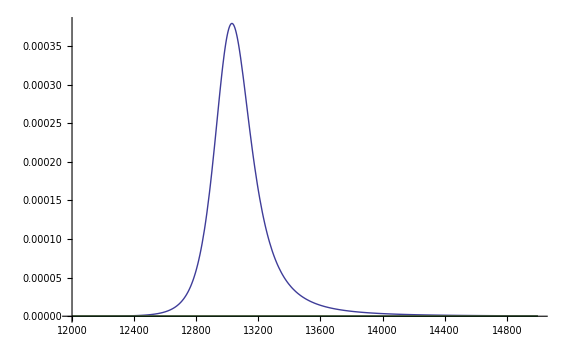

```mathematica
Plot[Evaluate@{spectrumM[ω,ham/.{c2->0.,r2->10.},0]⟦1⟧},{ω,12000.,15000.},PlotRange->All,Ticks->True,PlotStyle->Thick]
```

```mathematica
(Cos[1.5]+Sin[1.5])^2
```

1.14112

```mathematica
(-0.30116867893975674)^2
```

0.0907026

```mathematica
0.5403023058681398
```

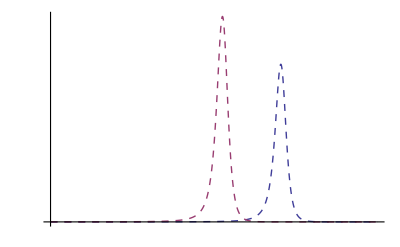

```mathematica
Plot[Evaluate@{0.8588799919401328spectrum[ω,ham/.{c2->0.,r2->8.},1,2,1]⟦1,1⟧,1.1411200080598674spectrum[ω,ham/.{c2->0.,r2->10.},1,2,1]⟦2,2⟧},{ω,10000.,15000.},PlotRange->All,Filling->None,Ticks->None,PlotStyle->{{Thick,Dashed},{Thick,Dashed}}]
```

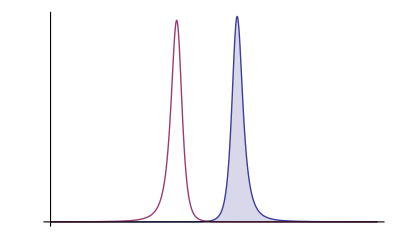

```mathematica
Plot[Evaluate@{spectrum[ω,ham/.{c2->0.,r2->8.},3,4,0]⟦1,1⟧,spectrum[ω,ham/.{c2->0.,r2->10.},3,4,1]⟦2,2⟧},{ω,10000.,15000.},PlotRange->All,Filling->{1->Bottom},Ticks->None,PlotStyle->Thick]
```

## Dynamics Generation (Full spectrum)

```mathematica
(* This generates systems of ODEs via classical master equation with the transfer rates calculated by the Foerster theories *)
(* Note in this program, we provide three means to measure the efficiency from the donors to the acceptors *)
ParallelTable[
ParallelTable[
SFrate[r2s,c2s]=With[{var=vars,r2=r2s,c2=c2s},SFTrate[hamfluc[var,r2,c2]]];
GFrate[r2s,c2s]=With[{var=vars,r2=r2s,c2=c2s},GFTrate[hamfluc[var,r2,c2]]];
npop[vars,r2s,c2s]=Flatten[
{
gfa=GFrate[r2s,c2s];
(* First method: calculate efficiency via exponential fit to the solutions to the master equations, focusing on acceptor populations *)

(*gf[t_]={gf1[t],gf2[t],gf3[t],gf4[t]};
systemgf=MapThread[#1==#2&,{gf'[t],gfa.gf[t]}];
initgf={gf1[0]==0.5,gf2[0]==0.5,gf3[0]==0,gf4[0]==0};
gfsol=DSolve[Join[systemgf,initgf],gf[t],t];
fitpoint=Union[{0},Table[2^-i,{i,40.,20.,-0.5}]];
{a,τ}/.FindFit[Table[{t,Sum[Flatten[gf[t]/.gfsol][[i]],{i,3,4}]},{t,fitpoint}],{a(1-Exp[-τ t])},{{a,0.5},{τ,0}},t]*)


(* Second method: calculate efficiency simply via the single rate of the rate-determining step *)
(*Max[{gfa⟦1,3⟧,gfa⟦1,4⟧,gfa⟦2,3⟧,gfa⟦2,4⟧}]}];*)

(* Third method: calculate efficiency by the equilibrium effective rate from the donors to the acceptors *)
Module[
{partitionfx=Exp[-β hamc[hamfluc[vars,r2s,c2s]]⟦1,1⟧]+Exp[-β hamc[hamfluc[vars,r2s,c2s]]⟦2,2⟧],u1=Exp[-β hamc[hamfluc[vars,r2s,c2s]]⟦1,1⟧],u2=Exp[-β hamc[hamfluc[vars,r2s,c2s]]⟦2,2⟧]},
u1/partitionfx(gfa⟦1,3⟧+gfa⟦1,4⟧)+u2/partitionfx(gfa⟦2,3⟧+gfa⟦2,4⟧)

]
}
];

npopsf[vars,r2s,c2s]=Flatten[
{sfa=SFrate[r2s,c2s];
(* First method: calculate efficiency via exponential fit to the solutions to the master equations, focusing on acceptor populations *)
(*sf[t_]={sf1[t],sf2[t],sf3[t],sf4[t]};
systemsf=MapThread[#1==#2&,{sf'[t],sfa.sf[t]}];
initsf={sf1[0]==0.5,sf2[0]==0.5,sf3[0]==0,sf4[0]==0};
sfsol=DSolve[Join[systemsf,initsf],sf[t],t];
fitpoint=Union[{0},Table[2^-i,{i,30.,20.,-0.5}]];
{a,τ}/.FindFit[Table[{t,Sum[Flatten[sf[t]/.sfsol][[i]],{i,3,4}]},{t,fitpoint}],{a(1-Exp[-τ t])},{{a,0.5},{τ,0}},t]*)

(* Second method: calculate efficiency simply via the single rate of the rate-determining step *)
(*Max[{sfa⟦1,3⟧,sfa⟦1,4⟧,sfa⟦2,3⟧,sfa⟦2,4⟧}]*)

(* Third method: calculate efficiency by the equilibrium effective rate from the donors to the acceptors *)
Module[
{partitionfx=Exp[-β hamfluc[vars,r2s,c2s]⟦1,1⟧]+Exp[-β hamfluc[vars,r2s,c2s]⟦2,2⟧],u1=Exp[-β hamfluc[vars,r2s,c2s]⟦1,1⟧],u2=Exp[-β hamfluc[vars,r2s,c2s]⟦2,2⟧]},
u1/partitionfx(sfa⟦1,3⟧+sfa⟦1,4⟧)+u2/partitionfx(sfa⟦2,3⟧+sfa⟦2,4⟧)

]
}];,{r2s,6.,14.,0.1},{c2s,0,0,1}];,{vars,1,realn,1}];
```

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

$Aborted

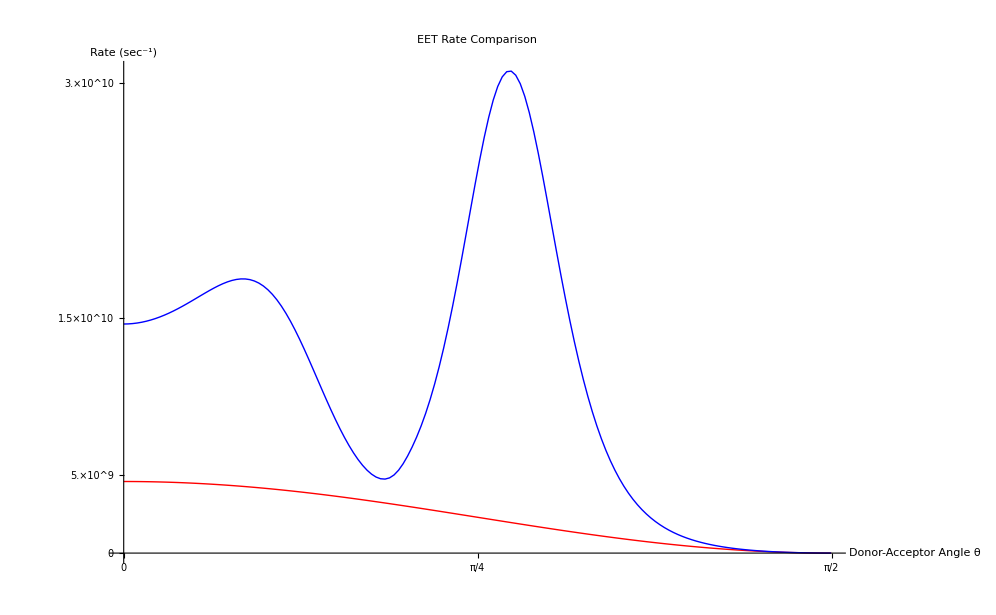

```mathematica
Show[{ListPlot[Partition[Flatten@Table[{r2,npopsf[1,9.,r2]},{r2,0,0.5π,0.01}],2],PlotStyle->{Red,Thick},Filling->None,Frame->False,GridLines->None,Joined->True,PlotRange->All],ListPlot[Partition[Flatten@Table[{r2,npop[1,9.,r2]},{r2,0,0.5π,0.01}],2],Joined->True,PlotStyle->{Blue,Thick},Filling->None,PlotRange->All]},PlotLabel->Style["EET Rate Comparison",24],AxesLabel->{"Donor-Acceptor Angle θ","Rate (sec^-1)"},FormatType->StandardForm,TicksStyle->Directive[Black,24],LabelStyle->Directive[Black,24],AxesStyle->Thick,Ticks->{{0,1/4 π,1/2 π},{0,5.0*10^9,1.5*10^10,3.0*10^10}}]
```

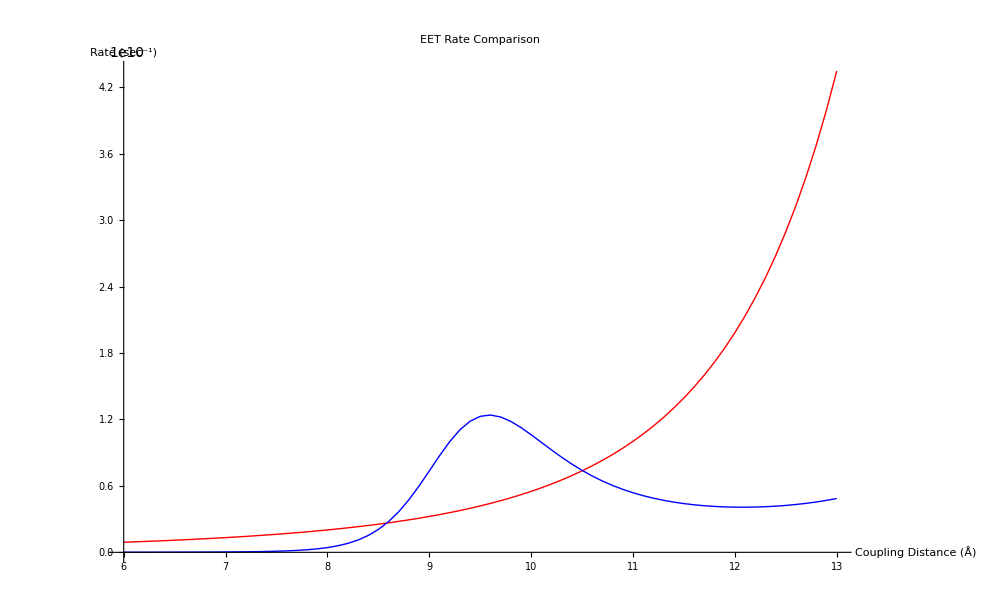

```mathematica
Show[{ListPlot[Partition[Flatten@Table[{r2,npopsf[1,r2,0]},{r2,6.,13.,0.1}],2],PlotStyle->{Red,Thick},Filling->None,Frame->False,GridLines->None,Joined->True,PlotRange->All],ListPlot[Partition[Flatten@Table[{r2,npop[1,r2,0]},{r2,6.,13.,0.1}],2],Joined->True,PlotStyle->{Blue,Thick},Filling->None,PlotRange->All]},PlotLabel->Style["EET Rate Comparison",24],AxesLabel->{"Coupling Distance (Å)","Rate (sec^-1)"},FormatType->StandardForm,TicksStyle->Directive[Black,24],LabelStyle->Directive[Black,24],AxesStyle->Thick,AxesOrigin->{6.,0}]
```

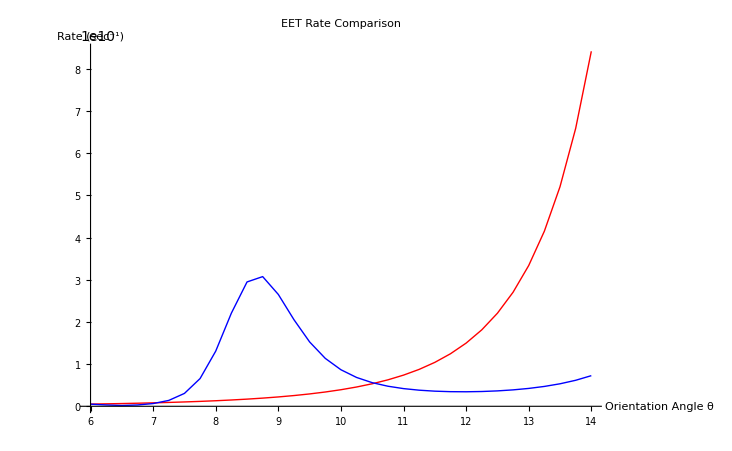

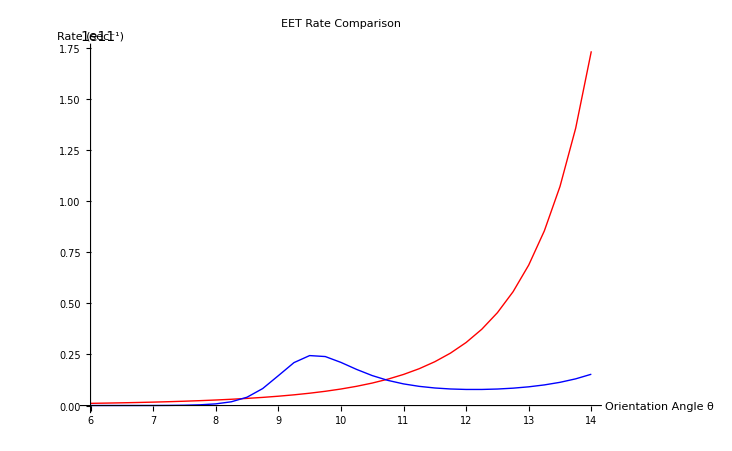

```mathematica
Show[{ListPlot[Partition[Flatten@Table[{r2,npopsf[1,r2,0.8]},{r2,6.,14.,0.25}],2],PlotStyle->{Red,Thick},Filling->None,Frame->False,GridLines->None,Joined->True,PlotRange->All],ListPlot[Partition[Flatten@Table[{r2,npop[1,r2,0.8]},{r2,6.,14.,0.25}],2],Joined->True,PlotStyle->{Blue,Thick},Filling->None,PlotRange->All]},PlotLabel->Style["EET Rate Comparison",24],AxesLabel->{"Orientation Angle θ","Rate (sec^-1)"},FormatType->StandardForm,TicksStyle->Directive[Black,24],LabelStyle->Directive[Black,24],AxesStyle->Thick]
Show[{ListPlot[Partition[Flatten@Table[{r2,npopsf[1,r2,0.]},{r2,6.,14.,0.25}],2],PlotStyle->{Red,Thick},Filling->None,Frame->False,GridLines->None,Joined->True,PlotRange->All],ListPlot[Partition[Flatten@Table[{r2,npop[1,r2,0.]},{r2,6.,14.,0.25}],2],Joined->True,PlotStyle->{Blue,Thick},Filling->None,PlotRange->All]},PlotLabel->Style["EET Rate Comparison",24],AxesLabel->{"Orientation Angle θ","Rate (sec^-1)"},FormatType->StandardForm,TicksStyle->Directive[Black,24],LabelStyle->Directive[Black,24],AxesStyle->Thick]
```

```mathematica
Show[{ListPlot[Partition[Flatten@Table[{r2,npopsf[1,r2,0.4]},{r2,6.,14.,0.25}],2],PlotStyle->{Red,Thick},Filling->None,Frame->False,GridLines->None,Joined->True,PlotRange->All],ListPlot[Partition[Flatten@Table[{r2,npop[1,r2,0.4]},{r2,6.,14.,0.25}],2],Joined->True,PlotStyle->{Blue,Thick},Filling->None,PlotRange->All]},PlotLabel->Style["EET Rate Comparison",24],AxesLabel->{"Orientation Angle θ","Rate (sec^-1)"},FormatType->StandardForm,TicksStyle->Directive[Black,24],LabelStyle->Directive[Black,24],AxesStyle->Thick]
```

```mathematica
gf=ToExpression@Import["~/Documents/Research/Arrangements_Mar.2010-/110504-gf.txt"];
sf=ToExpression@Import["~/Documents/Research/Arrangements_Mar.2010-/110504-sf.txt"];
delta=ToExpression@Import["~/Documents/Research/Arrangements_Mar.2010-/110504-delta.txt"];
```

```mathematica
Export["~/Documents/Research/Arrangements_Mar.2010-/110507-sf.txt",sf]
```

~/Documents/Research/Arrangements_Mar.2010-/110507-sf.txt

```mathematica
gf=Partition[Flatten@Table[{i,j,npop[1,i,j]},{i,6.,14.,0.5},{j,0,0.5π,0.05}],3];
sf=Partition[Flatten@Table[{i,j,npopsf[1,i,j]},{i,6.,14.,0.5},{j,0,0.5π,0.05}],3];
delta=Partition[Flatten@Table[{i,j,npop[1,i,j]-npopsf[1,i,j]},{i,6.,14.,0.5},{j,0,0.5π,0.05}],3];
```

```mathematica
FrameTicks->{{None,{-1/2,1/2}},{{0,Pi,2Pi,3Pi},None}}
```

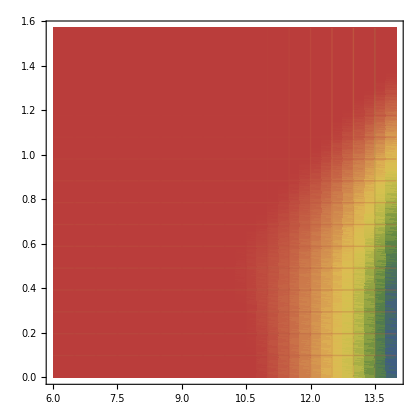

```mathematica
ListDensityPlot[delta,ColorFunction->"DarkRainbow",Mesh->True,PlotRange->All]
```

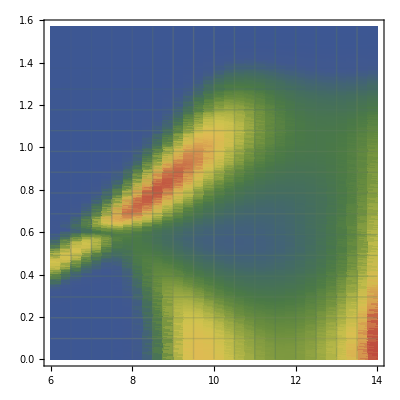

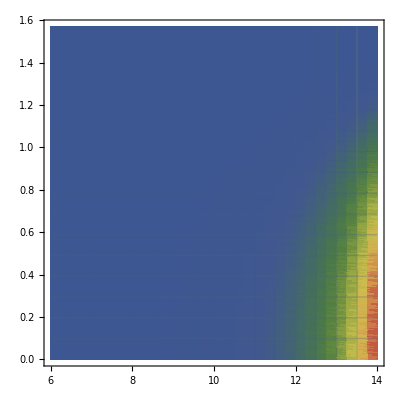

```mathematica
ListDensityPlot[gf,ColorFunction->"DarkRainbow",Mesh->True,PlotRange->All]
ListDensityPlot[sf,ColorFunction->"DarkRainbow",Mesh->True,PlotRange->All]
```

```mathematica
gf0504=ListPlot3D[gf,InterpolationOrder->3,Filling->Bottom,ColorFunction->"DarkRainbow",Ticks->{Automatic,{0,1/4 π,1/2 π},Automatic},ViewPoint->{-2.042,-1.233,2.400},AxesLabel->{"intracomplex distance, r (angstrom)","donor-acceptor angle, θ","rate (sec^-1)"},PlotLabel->"Generalized Foerster",FormatType->StandardForm];
sf0504=ListPlot3D[sf,InterpolationOrder->3,Filling->Bottom,ColorFunction->"DarkRainbow",Ticks->{Automatic,{0,1/4 π,1/2 π},Automatic},ViewPoint->{-2.042,-1.233,2.400},AxesLabel->{"intracomplex distance, r (angstrom)","donor-acceptor angle, θ","rate (sec^-1)"},PlotLabel->"Simple Foerster",FormatType->StandardForm];
```

```mathematica
combined0504=GraphicsGrid[{{sf0504,gf0504}},ImageSize->Full];
Export["~/Documents/Research/Arrangements_Mar.2010-/combined.bmp",combined0504]
```

~/Documents/Research/Arrangements_Mar.2010-/combined.bmp

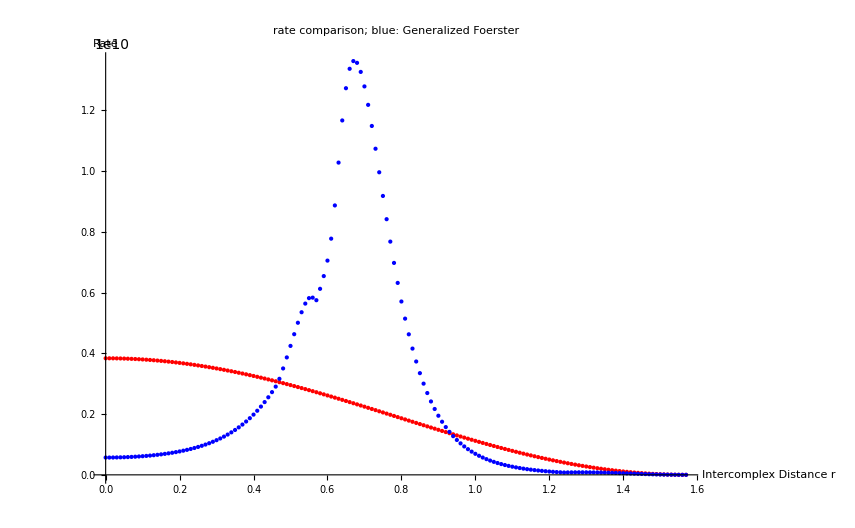

```mathematica
Show[{ListPlot[Partition[Flatten@Table[{r2,npopsf[1,r2]},{r2,0,0.5π,0.01}],2],PlotStyle->Red,Filling->None,Frame->False,GridLines->None,Joined->False,PlotRange->All],ListPlot[Partition[Flatten@Table[{r2,npop[1,r2]},{r2,0,0.5π,0.01}],2],Joined->False,PlotStyle->Blue,Filling->None,PlotRange->All]},PlotLabel->"rate comparison; blue: Generalized Foerster",AxesLabel->{"Intercomplex Distance r","Rate"}]
```

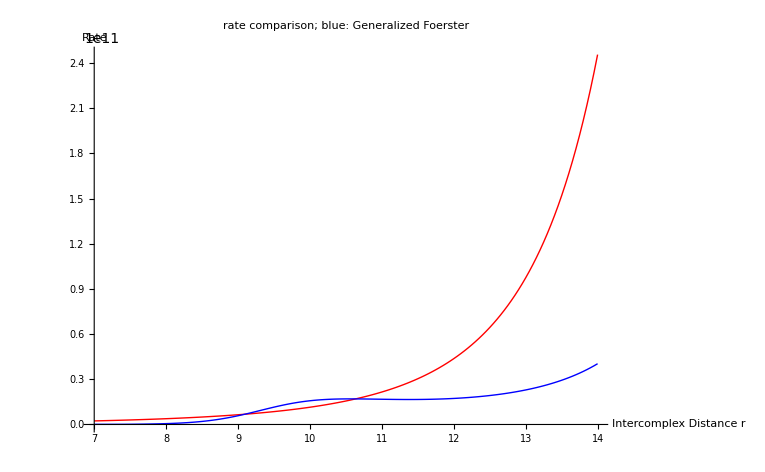

```mathematica
Show[{ListPlot[Partition[Flatten@Table[{r2,popsf[1,r2]},{r2,7.,14.,0.05}],2],PlotStyle->Red,Filling->None,Frame->False,GridLines->None,Joined->True],ListPlot[Partition[Flatten@Table[{r2,pop[1,r2]},{r2,7.,14.,0.05}],2],Joined->True,PlotStyle->Blue,Filling->None,PlotRange->All]},PlotLabel->"rate comparison; blue: Generalized Foerster",AxesLabel->{"Intercomplex Distance r","Rate"}]
```

## Calculation Results

```mathematica
showplot=1;
fig1=Show[Table[Flatten[Table[DiscretePlot[GFcoup[r2]⟦i,j⟧,{r2,6.,14.,0.05},Filling->None,Frame->True,PlotStyle->k,PlotRange->{Automatic,{-50,50}},PlotLabel->"D-A coupling; red:D+A+, blue:D+A-, green:D-A+, orange:D-A-",GridLines->Automatic],{i,1,2},{j,3,4},{k,{Red,Blue,Green,Orange}}],1]⟦k,k⟧,{k,1,4}]];
fig2=Show[Table[Flatten[Table[DiscretePlot[GFener[r2]⟦i,j⟧,{r2,6.,14.,0.05},Filling->None,Frame->True,PlotStyle->k,PlotRange->{All,{-1000,1000}},PlotLabel->"D-A energy difference; red:D+A+, blue:D+A-, green:D-A+, orange:D-A-",GridLines->Automatic],{i,1,2},{j,3,4},{k,{Red,Blue,Green,Orange}}],1]⟦k,k⟧,{k,1,4}]];
(* Change summation index from i:3;;4 and j:1;;2 if one wants to know the energy matching for backward transfer. *)


fig3=Show[Table[Table[DiscretePlot[GFenerM[r2]⟦i⟧,{r2,6.,14.,0.05},Filling->None,Frame->True,PlotStyle->k,PlotRange->All,Axes->{False,True},PlotLabel->"D-A energy; red:D+, blue:D-, green:A+, orange:A-",GridLines->Automatic],{i,1,4},{k,{Red,Blue,Green,Orange}}]⟦k,k⟧,{k,1,size}]];
fig4=Show[{DiscretePlot[popsf[showplot,r2],{r2,6.,14.,0.05},PlotStyle->Red,Filling->None,Frame->True,PlotRange->{Automatic,{0,1}},GridLines->Automatic,PlotLabel->"rate comparison; blue: Generalized Foerster"],DiscretePlot[pop[showplot,r2],{r2,6.,14.,0.05},PlotStyle->Blue,Filling->None,PlotRange->{Automatic,{0,1}}]}];
figfull=GraphicsGrid[{{fig4},{fig2},{fig1},{fig3}},ImageSize->Scaled[0.5]]

(*Export["~/Documents/Research/Arrangements_Mar.2010-/Figures/strange-2.pdf",figfull,ImageSize->Full];*)
```

## Rate Calculation (Gaussian-like spectrum)

```mathematica
(* Functions for calculating the rates *)
kFoerster[m_,n_,Hf_]:=kFoerster[m,n,Hf]=If[m==n,0,Sqrt[π]/(width  ℏ) Hf[[m,n]]^2 Exp[-(1/(4 β^2)) (2 λ+Hf[[n,n]]-Hf[[m,m]])^2]];

kGFoerster[m_,n_,Hf_]:=kGFoerster[m,n,Hf]=If[m==n,0,Sqrt[2 π]/(β ℏ) (hamc[Hf][[3]][[m,n]])^2 (hamc[Hf][[1]][[m]]^2+hamc[Hf][[1]][[n]]^2)^-0.5 Exp[-1/(2 β^2 (hamc[Hf][[1]][[m]]^2+hamc[Hf][[1]][[n]]^2)) (2 λ*hamc[Hf][[1]][[m]]+hamc[Hf][[3]][[n,n]]-hamc[Hf][[3]][[m,m]])^2]];

(* Below shows the components in calculating the generalized foerster rate, which is to see how each component contributes to the overall rate. *)
kGFcoup[m_,n_,Hf_]:=kGcoup[m,n,Hf]=(hamc[Hf][[3]][[m,n]]);
kGFener[m_,n_,Hf_]:=kGFener[m,n,Hf]=2 λ*hamc[Hf][[1]][[m]]+hamc[Hf][[3]][[n,n]]-hamc[Hf][[3]][[m,m]];
kGFenerM[m_,Hf_]:=kGFenerM[m,Hf]=hamc[Hf][[3]][[m,m]];
```

```mathematica
(* This generates systems of ODEs via classical master equation with the transfer rates calculated by the Foerster theories *)
Table[{
Table[{

SFrate[r2s]=With[{var=vars,r2=r2s},Table[kFoerster[i,j,hamfluc[var,r2]],{i,1,size},{j,1,size}]];
GFrate[r2s]=With[{var=vars,r2=r2s},Table[kGFoerster[i,j,hamfluc[var,r2]],{i,1,size},{j,1,size}]];
GFcoup[r2s]=With[{var=vars,r2=r2s},Table[kGFcoup[i,j,hamfluc[var,r2]],{i,1,size},{j,1,size}]];
GFenerM[r2s]=With[{var=vars,r2=r2s},Table[kGFenerM[i,hamfluc[var,r2]],{i,1,size}]];
GFener[r2s]=With[{var=vars,r2=r2s},Table[kGFener[i,j,hamfluc[var,r2]],{i,1,size},{j,1,size}]];


pop[vars,r2s]=Flatten[
{gfa=Chop[({{-(GFrate[r2s][[1,3]]+GFrate[r2s][[1,4]]),0,GFrate[r2s][[3,1]],GFrate[r2s][[4,1]]},{0,-(GFrate[r2s][[2,3]]+GFrate[r2s][[2,4]]),GFrate[r2s][[3,2]],GFrate[r2s][[4,2]]},{GFrate[r2s][[1,3]],GFrate[r2s][[2,3]],-(GFrate[r2s][[3,1]]+GFrate[r2s][[3,2]]),0},{GFrate[r2s][[1,4]],GFrate[r2s][[2,4]],0,-(GFrate[r2s][[4,1]]+GFrate[r2s][[4,2]])}}),10^-10];
gf[t_]={gf1[t],gf2[t],gf3[t],gf4[t]};
systemgf=MapThread[#1==#2&,{gf'[t],gfa.gf[t]}];
initgf={gf1[0]==0.5,gf2[0]==0.5,gf3[0]==0,gf4[0]==0};
gfsol=DSolve[Join[systemgf,initgf],gf[t],t];
(*data=FunctionInterpolation[Evaluate[Simplify[Total@gf[t][[1;;dsize]]/.gfsol]],{t,0,Max[GFrate[[sum]]]^-1}];*)Evaluate[Sum[Flatten[gf[t]/.gfsol][[i]],{i,3,4}]]/.{t->τt}}];
popsf[vars,r2s]=Flatten[
{sfa=Chop[({{-(SFrate[r2s][[1,2]]+SFrate[r2s][[1,3]]+SFrate[r2s][[1,4]]),SFrate[r2s][[2,1]],SFrate[r2s][[3,1]],SFrate[r2s][[4,1]]},{SFrate[r2s][[1,2]],-(SFrate[r2s][[2,1]]+SFrate[r2s][[2,3]]+SFrate[r2s][[2,4]]),SFrate[r2s][[3,2]],SFrate[r2s][[4,2]]},{SFrate[r2s][[1,3]],SFrate[r2s][[2,3]],-(SFrate[r2s][[3,1]]+SFrate[r2s][[3,2]]+SFrate[r2s][[3,4]]),SFrate[r2s][[4,3]]},{SFrate[r2s][[1,4]],SFrate[r2s][[2,4]],SFrate[r2s][[3,4]],-(SFrate[r2s][[4,1]]+SFrate[r2s][[4,2]]+SFrate[r2s][[4,3]])}}),10^-10];
sf[t_]={sf1[t],sf2[t],sf3[t],sf4[t]};
systemsf=MapThread[#1==#2&,{sf'[t],sfa.sf[t]}];
initsf={sf1[0]==0.5,sf2[0]==0.5,sf3[0]==0,sf4[0]==0};
sfsol=DSolve[Join[systemsf,initsf],sf[t],t];
(*data=FunctionInterpolation[Evaluate[Simplify[Total@gf[t][[1;;dsize]]/.gfsol]],{t,0,Max[GFrate[[sum]]]^-1}];*)Evaluate[Sum[Flatten[sf[t]/.sfsol][[i]],{i,3,4}]]/.{t->τt}}];
(*rslt[vars]=FindMaximum[{Interpolation[Table[Flatten[{r2s,pop[vars,r2s]}],{r2s,7.,12.,1.}]][x],7.<x<12.},{x,10.},MaxIterations->1000];*)},{r2s,6.,14.,0.05}];},{vars,1,realn,1}];
```